```mathematica
SetDirectory[NotebookDirectory[]];
Directory[]
```

```mathematica
dataSet=Import["TrainingData.csv"];
```

```mathematica
dataSet⟦;;15⟧//TableForm
(*The firts two colums (input variables) are the number concentration and liquid water content*)
(*The third column is the normalized theoretical autoconversion rate (for drop number concentration or liquid water content)*)
```

675.367 | 1.08233×10^-6 | 0.204868
370.009 | 6.49732×10^-7 | -0.230523
854.939 | 6.90575×10^-7 | -0.54323
110.573 | 7.76996×10^-7 | 1.205
762.408 | 4.96066×10^-7 | -0.571896
181.638 | 1.03478×10^-6 | 2.63385
1245.26 | 9.46978×10^-7 | -0.526479
496.535 | 3.93788×10^-7 | -0.568308
954.435 | 7.87758×10^-7 | -0.528182
388.157 | 7.94807×10^-7 | 0.135153
1015.51 | 1.16151×10^-6 | -0.224609
526.191 | 6.96915×10^-7 | -0.381314
92.0137 | 2.17611×10^-7 | -0.510271
378.092 | 5.16254×10^-7 | -0.460982
460.42 | 3.01436×10^-7 | -0.576392

```mathematica
(*Check the number of samples*)
```

```mathematica
Dimensions[dataSet]
```

{100000,3}

```mathematica
(* Calculating the number of samples in training dataset: 80% of the data*)
n=Length[dataSet];
trainN=Floor[0.8 n];
(*Splitting the data into training and test datasets*)
```

```mathematica
RandomSeed[123];
{dataTrain,dataTest}=TakeDrop[RandomSample@dataSet,trainN];
Dimensions[dataTrain]
Dimensions[dataTest]
```

{80000,3}

{20000,3}

```mathematica
xTrain=dataTrain⟦All,1;;2⟧;
yTrain=dataTrain⟦All,3⟧;
xTest=dataTest⟦All,1;;2⟧;
yTest=dataTest⟦All,3⟧;
```

```mathematica
(*Normalizing the data*)
```

```mathematica
xTrainStandardized=Transpose@Map[Standardize,Transpose[xTrain]];
Mean[xTrainStandardized]
StandardDeviation[xTrainStandardized]
```

```mathematica
{-9.912071163853398*^-17,2.0605739337042904*^-17}
```

{-9.91207×10^-17,2.06057×10^-17}

```mathematica
xTestStandardized=Transpose@Table[(xTest[[All,i]]-Mean[xTrain][[i]])/StandardDeviation[xTrain][[i]],{i,2}];

Mean[xTestStandardized]//N
StandardDeviation[xTestStandardized]//N
```

{-0.0151027,0.0190923}

{1.00094,1.00716}

```mathematica
train=Table[xTrainStandardized⟦i,All⟧->yTrain⟦i⟧,{i,trainN}];
Dimensions[train]
train⟦;;1⟧ //N (*Show first sample*)
```

{80000}

{{0.349685,0.346478}→-0.353125}

```mathematica
test=Table[xTestStandardized⟦i,All⟧->yTest⟦i⟧,{i,Length[yTest]}];
Dimensions[test]
test⟦;;1⟧//N
```

{20000}

{{1.40324,1.46396}→-0.1976}

```mathematica
{{0.3047552205227433,-1.1388604264767144}->-0.607034282785124}
```

{{0.304755,-1.13886}→-0.607034}

```mathematica
{{-0.7797882489403849,0.10372112993392912,-0.11630626794584462,-0.5511119722191015,-0.9074918357138656,0.21174716158966625,-1.6068020382128585,0.801765533410605,-1.0444984977798342,2.1106413897150946}->6.6}
```

{{-0.779788,0.103721,-0.116306,-0.551112,-0.907492,0.211747,-1.6068,0.801766,-1.0445,2.11064}→6.6}

```mathematica
(*Creating the network*)
net=NetChain[{20,Ramp,20,Ramp,20,Ramp,1},"Input"->2,"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
(*Initializing Weights and Biases*)
```

```mathematica
net=NetInitialize[net,Method->{"Random","Weights"->0.01,"Biases"->0}]
```

NetChain[<>]

```mathematica
(*Training the network*)
```

```mathematica
trained=NetTrain[net,train,LossFunction->MeanAbsoluteLossLayer[],BatchSize->32,TargetDevice->"CPU",Method->"RMSProp",MaxTrainingRounds->25]
```

NetChain[<>]

NetChain[<>]

NetChain[<>]

«2 more identical outputs»

```mathematica
(*Testing the model*)
```

```mathematica
predicted=trained[xTestStandardized];
```

```mathematica
actualPredicted=Table[{yTest⟦i⟧,predicted⟦i⟧},{i,Length[yTest]}];
```

```mathematica
{yTest⟦13⟧,predicted⟦13⟧}
```

{4.86328,5.00209}

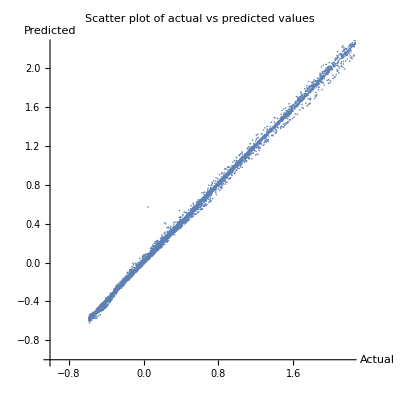

```mathematica
ListPlot[actualPredicted,PlotLabel->"Scatter plot of actual vs predicted values",AxesOrigin->{-1,-1},AspectRatio->1,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
(*Calculate the absolute values of the differences*)
```

```mathematica
actualNegativePredicted=Table[{yTest⟦i⟧,-predicted⟦i⟧},{i,Length[yTest]}];
```

```mathematica
Mean[Abs[Plus@@@actualNegativePredicted]]
```

0.0128354

```mathematica
Dimensions[actualPredicted]
Export["ActualvsPredicted.txt",actualPredicted]
```

{20000,2}

ActualvsPredicted.txt